Linear Multivariate Regression

{-0.267864,-0.00111714,0.00563934,-0.00559228,0.0187985,0.526525}

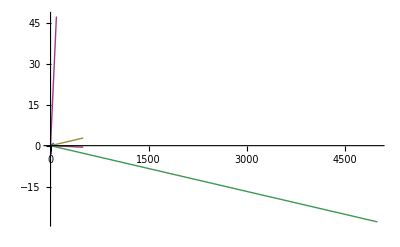

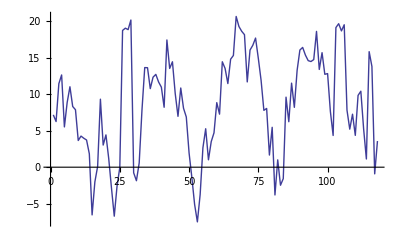

Mean Error →8.59538

```mathematica
Multivariate Linear Regression

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

X = autoMPGDataSet[[1;;testSetLength,2;;7]];
Y=autoMPGDataSet[[1;; testSetLength,1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y)



predictedSeperator1 = Table[β[[1]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[2]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[4]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[5]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[6]]*featureValue,{featureValue,90}];
ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]


predictedMPG = Table[β  . autoMPGDataSet[[i,2;;7]],{i,testSetLength+1,Length[autoMPGDataSet]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-Y[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Mean[error]
```

### Multivariate Linear Regression w/ Threshold (w0)

{-14.5353,-0.329859,0.00767843,-0.000391356,-0.00679462,0.0852732,0.753367}

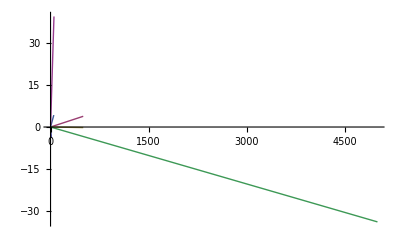

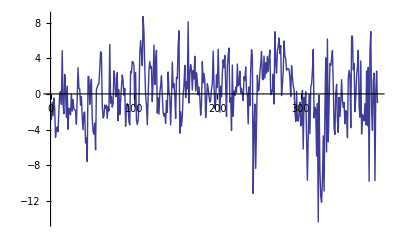

Mean Error →2.10686×10^-12

```mathematica
autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
X = autoMPGDataSet[[1;;Length[autoMPGDataSet],2;;7]];
unaryRow=Table[1,{Length[autoMPGDataSet]}];
X = Insert[X//Transpose,unaryRow,1]//Transpose;

Y=autoMPGDataSet[[1;; Length[autoMPGDataSet],1]];

β = Inverse[Transpose[X] . X ]  . (Transpose[X] . Y)

predictedMPG = Table[β  . X[[i,All]],{i,Length[X]}];

predictedSeperator1 = Table[β[[2]]*featureValue,{featureValue,12}];
predictedSeperator2 = Table[β[[3]]*featureValue,{featureValue,500}];
predictedSeperator3 = Table[β[[4]]*featureValue,{featureValue,500}];
predictedSeperator4 = Table[β[[5]]*featureValue,{featureValue,5000}];
predictedSeperator5 = Table[β[[6]]*featureValue,{featureValue,50}];
predictedSeperator6 = Table[β[[7]]*featureValue,{featureValue,90}];
ListLinePlot[{predictedSeperator1,predictedSeperator2,predictedSeperator3,predictedSeperator4,predictedSeperator5,predictedSeperator6}]

testSetLength = 274;
predictedMPG = Table[β  . autoMPGDataSet[[i,2;;7]],{i,testSetLength+1,Length[autoMPGDataSet]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-Y[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Mean[error]
```

### Quadratic regression

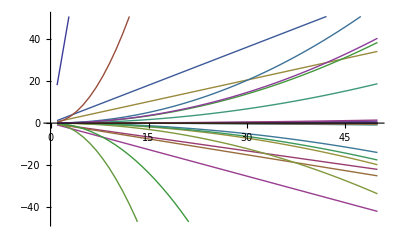

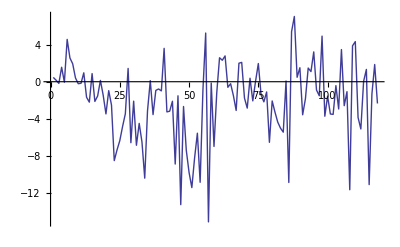

Mean Error →-2.0725

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤2,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];

Y=autoMPGDataSet[[1;; testSetLength,1]];

β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);


vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Mean[error]
```

### 3rd Degree Polynomial Regression Model

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤3,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose ;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];
Y=autoMPGDataSet[[1;; testSetLength,1]];


β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);



vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Mean[error]
```

### 4th Degree Polynomial Regression Model

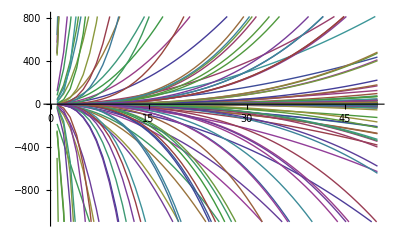

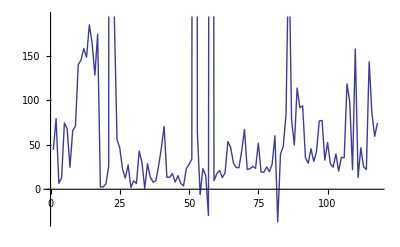

Mean Error →154.767

```mathematica
Off[Inverse::luc]

Multisets[l_List,k_]:=Union[Sort/@Flatten[Outer[List,Sequence@@Table[l,{k}]],k-1]]
Multisets[n_,k_]:=Multisets[Range[n],k]

autoMPGDataSet = Import["D:\\auto-mpg.data","CSV"];
testSetLength = 274;

listCombo = {};

For[i=1,i≤4,i++,listCombo = Union[listCombo,Multisets[{2,3,4,5,6,7},i]]];

newX = {};
For[vectorComponent=1,vectorComponent≤ Length[listCombo],vectorComponent++,
componentRow = Table[
Product[
autoMPGDataSet[[instance,listCombo[[vectorComponent,i]]]],
{i,1,Length[listCombo[[vectorComponent]]]}],
{instance,1,Length[autoMPGDataSet]}];
newX = Append[newX,componentRow];
]
newX = newX //Transpose ;
testX = newX[[testSetLength+1;;Length[autoMPGDataSet],All]] ;
newX = newX[[1;;testSetLength,All]];
Y=autoMPGDataSet[[1;; testSetLength,1]];


β = Inverse[Transpose[newX] . newX ]  . (Transpose[newX] . Y);



vectorsInPredictor =  Table[
Table[
β[[vectorComponent]]*featureValue^Floor[ Log[8,vectorComponent]+1],
{featureValue,1,50}],
{vectorComponent,1,Length[β]}];


ListLinePlot[vectorsInPredictor]

predictedMPGTraining = Table[β  . newX[[i,All]],{i,Length[newX]}];

predictedMPG = Table[β  . testX[[i,All]],{i,1,Length[testX]}];
actualMPG = autoMPGDataSet[[testSetLength+1;; Length[autoMPGDataSet],1]];
error = Table[predictedMPG[[i]]-actualMPG[[i]],{i,1,Length[predictedMPG]}];
ListLinePlot[error]
"Mean Error "  -> Mean[error]
```